```mathematica
a={{1,2,3},{1,2,4}} ;
```

```mathematica
a// MatrixForm
```

(1 | 2 | 3
1 | 2 | 4)

```mathematica
a
```

```mathematica
MatrixForm[Table[Subscript[f, i,j],{i,0,3},{j,0,3}]]
```

(f_(0,0) | f_(0,1) | f_(0,2) | f_(0,3)
f_(1,0) | f_(1,1) | f_(1,2) | f_(1,3)
f_(2,0) | f_(2,1) | f_(2,2) | f_(2,3)
f_(3,0) | f_(3,1) | f_(3,2) | f_(3,3))

```mathematica
RandomInteger[{-10,5},{3,2}] //MatrixForm
```

(0 | 5
-3 | -2
-2 | -3)

```mathematica
x1={1,2,3};
x2={3,2,4};
X={x1, x2, {4,5,6}};
```

```mathematica
X//MatrixForm
```

(1 | 2 | 3
3 | 2 | 4)

```mathematica
IdentityMatrix[3] //MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
DiagonalMatrix[x1,1] // MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 3
0 | 0 | 0 | 0)

```mathematica
X [[2,3]]
```

4

```mathematica
X[[3]]
```

{4,5,6}

```mathematica
X[[All,1]]
```

{1,3,4}

```mathematica
X[[2;;3, 1;;2]]
```

{{3,2},{4,5}}

```mathematica
X[[2;;3,{1,3}]]
```

{{3,4},{4,6}}

```mathematica
X.a
```

Dot::dotsh: Tensors {{1,2,3},{3,2,4},{4,5,6}} and {{1,2,3},{1,2,4}} have incompatible shapes.

{{1,2,3},{3,2,4},{4,5,6}}.{{1,2,3},{1,2,4}}

```mathematica
a.X
```

{{19,21,29},{23,26,35}}

```mathematica
x1.x2
```

19

```mathematica
Cross[x1,x2]
```

{2,5,-4}

```mathematica
MatrixPower[X,2]
```

{{19,21,29},{25,30,41},{43,48,68}}

```mathematica
Dimensions[X]
```

{3,3}

```mathematica
q=RandomInteger[{-10,10},{100,100}]
```

{1}
 |  |  |  |

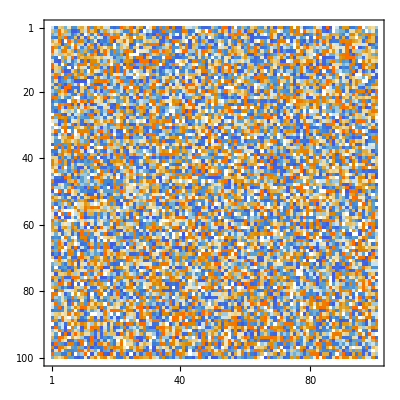

```mathematica
q// MatrixPlot
```

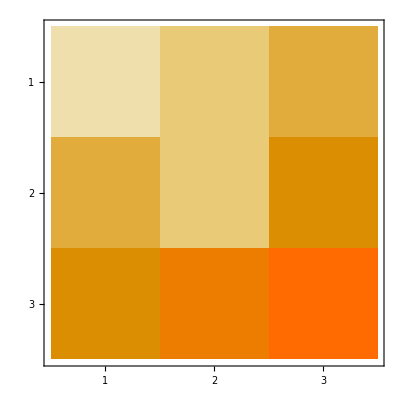

```mathematica
MatrixPlot[X]
```

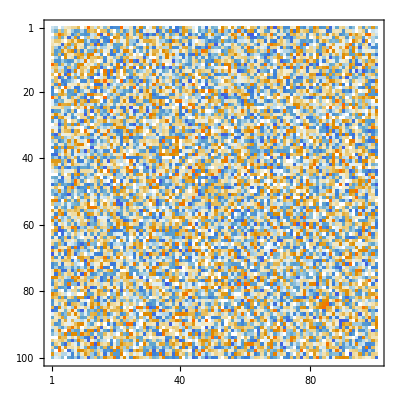

```mathematica
(q+Transpose[q]) // MatrixPlot
```

```mathematica
Det[X]
```

9

```mathematica
Inverse[X]
```

{{-8/9,1/3,2/9},{-2/9,-2/3,5/9},{7/9,1/3,-4/9}}

```mathematica
b={1,1,1}
```

{1,1,1}

```mathematica
LinearSolve[X,b]
```

{-1/3,-1/3,2/3}

```mathematica
Inverse[X].b
```

{-1/3,-1/3,2/3}

```mathematica
b1={{1},{1},{1}}
```

{{1},{1},{1}}

```mathematica
q=Join[X,b1,2]
```

{{1,2,3,1},{3,2,4,1},{4,5,6,1}}

```mathematica
q//RowReduce // MatrixForm
```

(1 | 0 | 0 | -1/3
0 | 1 | 0 | -1/3
0 | 0 | 1 | 2/3)

```mathematica
s=DiagonalMatrix[Table[0.1,{i,0,10}]];
```

```mathematica
s//MatrixForm (*Невырожденная матрица, но её определитель очень близок к 0, т.е. она близка к вырожденной*)
```

(0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1)

```mathematica
Det[s]
```

1.×10^-11

```mathematica
Norm[s,2]*Norm[Inverse[s],2] (*Cчитаем число обусловленности*)
```

1.

```mathematica
A={{1,10},{100, 1001}}
```

{{1,10},{100,1001}}

```mathematica
VectorAngle[A[[1]],A[[2]]] //N
```

0.000098912

```mathematica
b={11,1101};
```

```mathematica
LinearSolve[A,b]
```

{1,1}

```mathematica
b1={11.01,1101}
```

{11.01,1101}

```mathematica
LinearSolve[A,b1]
```

{11.01,4.42354×10^-14}

```mathematica
Chop[%]
```

{11.01,0}

```mathematica
Norm[A,2]*Norm[Inverse[A],2] // N
```

1.0121×10^6

```mathematica
Det[A]
```

1

```mathematica
{s,p,r} = LUDecomposition[X];
```

```mathematica
p (*матрица перестановок*)
```

{1,3,2}

```mathematica
как получить из s матрицы p и r
```

```mathematica
f=Table[1,{i,1,3}, {i,1,3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
UpperTriangularize[f]
```

{{1,1,1},{0,1,1},{0,0,1}}

```mathematica
s.
```